```mathematica
二重极限的存在性
```

```mathematica
Plot3D[(x^2-y^2)/(x^2+y^2),{x,-1,1},{y,-1,1},
Boxed->False,Axes->False,
Mesh->None,MeshStyle->{{White,Opacity[0.5]},{White,Opacity[0.5]}},
BoundaryStyle->None,
PlotPoints->20,
ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
Plot3D[(x^2-y^2)/(x^2+y^2),{x,-1,1},{y,-1,1},
Boxed->False,Axes->None,
Mesh->10,MeshStyle->{Black,Opacity[0.7]},
BoundaryStyle->None,
PlotPoints->20,
ColorFunction->"DarkRainbow",MeshFunctions->{#3&},Mesh->12]
```

-Graphics3D-

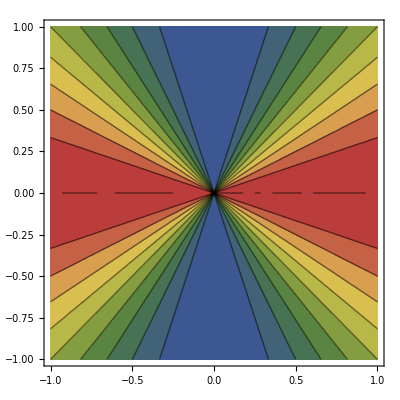

```mathematica
ContourPlot[(x^2-y^2)/(x^2+y^2),{x,-1,1},{y,-1,1},ColorFunction->"DarkRainbow"]
```

```mathematica
Plot3D[(x*y)/(x^2+y^2),{x,-1,1},{y,-1,1},
Boxed->False,Axes->None,
Mesh->10,MeshStyle->{Black,Opacity[0.7]},
BoundaryStyle->None,
PlotPoints->20,
ColorFunction->"DarkRainbow",MeshFunctions->{#3&},Mesh->12]
```

-Graphics3D-

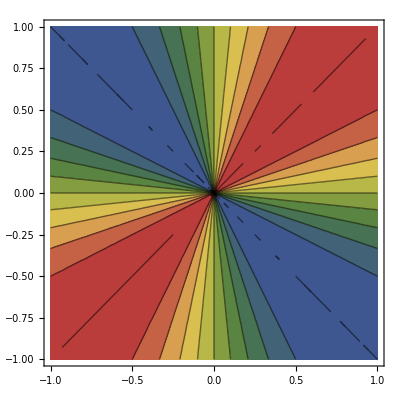

```mathematica
ContourPlot[(x*y)/(x^2+y^2),{x,-1,1},{y,-1,1},ColorFunction->"DarkRainbow"]
```

```mathematica
Plot3D[(x^2y)/(x^2+y^2),{x,-1,1},{y,-1,1},
Boxed->False,Axes->None,
Mesh->10,MeshStyle->{Black,Opacity[0.7]},
BoundaryStyle->None,
PlotPoints->20,
ColorFunction->"DarkRainbow",MeshFunctions->{#3&},Mesh->12]
```

-Graphics3D-

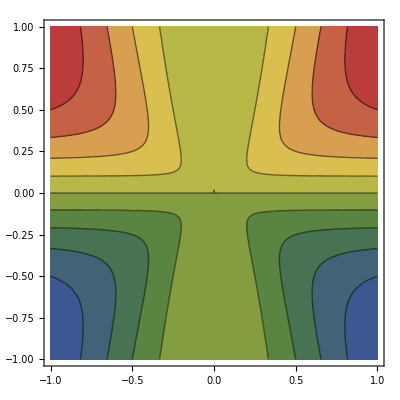

```mathematica
ContourPlot[(x^2*y)/(x^2+y^2),{x,-1,1},{y,-1,1},ColorFunction->"DarkRainbow"]
```

```mathematica
Plot3D[(x*y)/(x+y),{x,-1,1},{y,-1,1},
Boxed->False,Axes->None,
Mesh->10,MeshStyle->{Black,Opacity[0.7]},
BoundaryStyle->None,
PlotPoints->80,PlotRange->{-10,10},
ColorFunction->"DarkRainbow",MeshFunctions->{#3&},Mesh->12,RegionFunction->Function[{x,y,z},x>y||x<y]]
```

-Graphics3D-

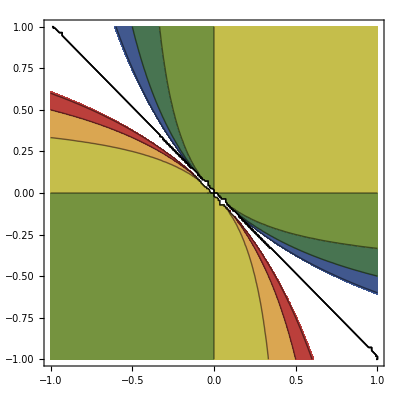

```mathematica
ContourPlot[(x*y)/(x+y),{x,-1,1},{y,-1,1},ColorFunction->"DarkRainbow"]
```

```mathematica
PolarPlot[{0.5(Cos[t]+Sin[t]),Cos[t]+Sin[t],1.5(Cos[t]+Sin[t]),2(Cos[t]+Sin[t]),
-0.5(Cos[t]+Sin[t]),-Cos[t]-Sin[t],-1.5(Cos[t]+Sin[t]),-2(Cos[t]+Sin[t])},{t,0,2Pi}]
```